### Meta Images

#### Avatar

```mathematica
Graphics[{Circle[],Text[Style["E",24,Bold,FontFamily->"Helvetica"],{0,-0.25}]},ImageSize->30]
```

-Graphics-

```mathematica
Graphics[{Circle[],Text[Style["尤",24,Bold,FontFamily->"Helvetica"],{0,0}]},ImageSize->30]
```

-Graphics-

#### Word Cloud

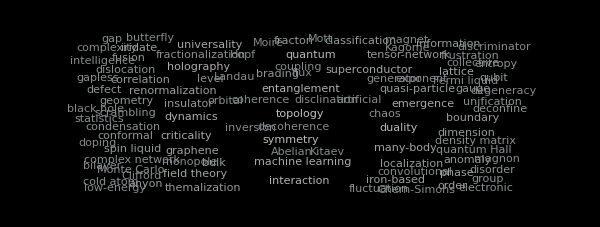

```mathematica
Block[{R,g},
SetOptions[$FrontEnd,DefaultStyleDefinitions->"Default.nb"];
R=Rectangle[{-1,-0.38},{1,0.38}];
g=WordCloud[<|"topology"->12,"symmetry"->11,"duality"->10,"quantum"->10,"entanglement"->9,"interaction"->9,"holography"->8,"dynamics"->8,"machine learning"->7,"emergence"->7,"universality"->7,"criticality"->7,"lattice"->6,"many-body"->6,"field theory"->6,"superconductor"->6,"order"->5,"phase"->5,"renormalization"->5,"graphene"->5,"iron-based"->5,"iridate"->5,"localization"->4,"themalization"->4,"spin liquid"->4,"insulator"->4,"information"->4,"tensor-network"->4,"dimension"->4,"transition"->1,"correlation"->4,"classification"->4,"bulk"->4,"boundary"->4,"anyon"->4,"fracton"->4,"quasi-particle"->4,"geometry"->3,"gauge"->3,"fusion"->3,"brading"->3,"defect"->3,"anomaly"->3,"conformal"->3,"qubit"->3,"gap"->2,"gapless"->2,"chaos"->2,"level"->2,"statistics"->2,"orbital"->2,"complex network"->2,"unification"->2,"group"->2,"frustration"->2,"fractionalization"->2,"deconfine"->2,"entropy"->2,"electronic"->2,"disorder"->2,"dislocation"->2,"condensation"->2,"cold atom"->2,"quantum Hall"->2,"scrambling"->2,"fluctuation"->2,"Fermi liquid"->1,"Monte Carlo"->2,"density matrix"->2,"inversion"->1,"exponent"->1,"spinon"->1,"spectrum"->1,"twist defect"->1,"disclination"->1,"Clifford"->1,"stablizer"->1,"thermalization"->1,"superfluid"->1,"string-net"->1,"spin-orbit"->1,"coupling"->1,"sign problem"->1,"complexity"->1,"Pati-Salam"->1,"Chern-Simons"->1,"oxides"->1,"optical"->1,"non-Abelian"->1,"Mott"->1,"magnon"->1,"magnet"->1,"Landau"->1,"Kitaev"->1,"Kagome"->1,"flux"->1,"vortex"->1,"monopole"->1,"Hopf"->1,"doping"->1,"degeneracy"->1,"protection"->1,"collective"->1,"tensor category"->1,"scaling"->1,"Abelian"->1,"telepotation"->1,"protocol"->1,"black hole"->1,"supersymmetry"->1,"butterfly"->1,"bilayer"->1,"Moire"->1,"neutron"->1,"scattering"->1,"photoemission"->1,"artificial"->1,"intelligence"->1,"coherence"->1,"decoherence"->1,"low-energy"->1,"pocket"->1,"supervised"->1,"unsupervised"->1,"generator"->1,"discriminator"->1,"recurent"->1,"convolutional"->1|>,R,Background->Black,ColorFunction->(ColorData["GrayTones",0.6+0.2#]&),ImageSize->600];
SetOptions[$FrontEnd,DefaultStyleDefinitions->"CMU Article.nb"];
g]
```

#### Research

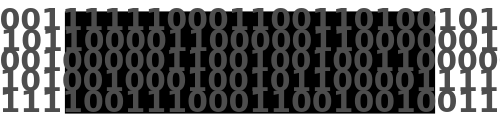

```mathematica
Graphics[{{Black,Rectangle[{0,0},{4,1}]},{GrayLevel[0.3],Table[Text[Style[StringJoin[ToString/@RandomChoice[{0,1},{30}]],30,Bold,FontFamily->"Helvetica"],{2,y},{0,0.15}],{y,0.1,0.9,0.2}]}},PlotRangeClipping->True,PlotRangePadding->None,ImageSize->500]
```

#### Search

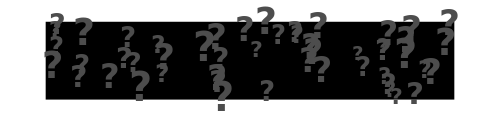

```mathematica
Graphics[{{Black,Rectangle[{0,0},{4,1}]},{GrayLevel[0.3],MapThread[Text[Style["?",#1,Bold,FontFamily->"Helvetica"],{4,1}#2]&,{RandomInteger[{20,40},#],RandomReal[{0,1},{#,2}]}&@50]}},PlotRange->{{0,4},{0,1}},PlotRangeClipping->True,PlotRangePadding->None,ImageSize->500]
```

## Posts

### Moire Superlattice

#### tBLG

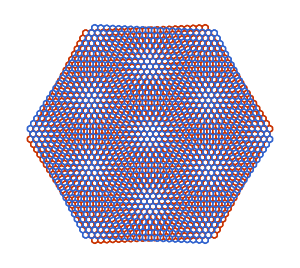

```mathematica
Block[{G},
(* G is a graph for a monolayer graphene *)
G=Block[{L=20,vs,es},
{{vs},{es}}=Last@Reap[Do[Block[{Rs,b},
Rs=({{Sqrt[3],3},{-Sqrt[3],3}}/2).RotationMatrix[θ];
b=l{1,0}+m{-1,1}/2+{1,1}/3;
If[OddQ[m],
b=b-{1,1}/6;
Sow[b.Rs<->(b+{2,-1}/3).Rs,"e"];
Sow[b.Rs<->(b+{-1,2}/3).Rs,"e"];
Sow[b.Rs<->(b+{-1,-1}/3).Rs,"e"],
If[m==0,Sow[b.Rs<->(b+{1,-2}/3).Rs,"e"]]];
Sow[b.Rs,"v"];],{l,0,L},{m,0,2l},{θ,Range[6]π/3}],{"v","e"}];
Graph[vs,es,VertexCoordinates->vs]];
Block[{g,θ=5°},
g=GraphicsComplex[VertexList[G],Line[First/@Most@ArrayRules@AdjacencyMatrix[G]]];
Graphics[{AbsoluteThickness[1],{Red,Rotate[g,θ/2,{0,0}]},{Blue,Rotate[g,-θ/2,{0,0}]}},ImageSize->300]]]
```